Routines for YODA plotting

from: https://yoda.hepforge.org/trac/wiki/DataFormat

```mathematica
<<(NotebookDirectory[]<>"../../atom_mathematica.m")
```

```mathematica
Zee=(GetYodaRaw[NotebookDirectory[]<>"Zee.yoda"]);
CMSee=(GetYodaRaw[NotebookDirectory[]<>"CMS_Zee.yoda"]);
```

1 Imported ..Scatter2D..  /REF/d01-x01-y01

2 Imported ..Histo1D..  /CMS_1402_0923/Mmm/0

1 Imported ..Histo1D..  /CMS_1402_0923/Mee/0

This contains Hist1D objects:

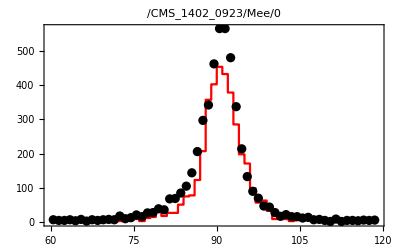

```mathematica
Fig1=HistogramPlot[Zee[[1]],PlotStyle->{Red}];
Fig2=ScatterPlot[CMSee[[1]],PlotStyle->{Black}];
Show[{Fig1,Fig2}]
```

```mathematica
Zmm=(GetYodaRaw[NotebookDirectory[]<>"Zmm.yoda"]);
CMSmm=(GetYodaRaw[NotebookDirectory[]<>"CMS_Zmm.yoda"]);
```

1 Imported ..Histo1D..  /CMS_1402_0923/Mee/0

2 Imported ..Histo1D..  /CMS_1402_0923/Mmm/0

1 Imported ..Scatter2D..  /REF/d01-x01-y01

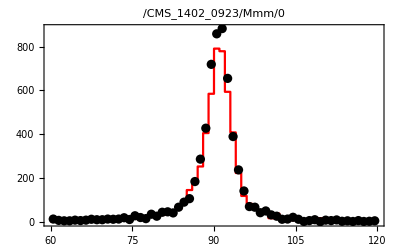

```mathematica
Fig1=HistogramPlot[Zmm[[2]],PlotStyle->{Red}];
Fig2=ScatterPlot[CMSmm[[1]],PlotStyle->{Black}];
Show[{Fig1,Fig2}]
```